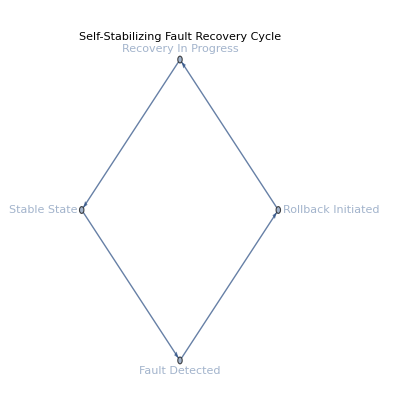
Æthernet: N2N Lattice with Reserved Path and Hamming Overlay | 
-Graphics- | 
-Graphics- | 
Atomic Ethernet Key Concepts
- Bipartite Token Coherence Protocol, not source-destination
- No message retry; failure handled by logical reversal
- Full erasure of prior attempts before retry
- Forward and reversal states are jointly managed by both endpoints
- Time-reversal is a logical rollback with no evidence of failure
- Lossless link assumption enables exactly-once semantics
- Simplifies recovery, enhances security by design |

```mathematica
Module[{meshDim=5,nodeRadius=0.3,meshCoords,meshEdges,reservedPathEdges,trafficClusters,trafficClusterColors,hammingEdges,hammingEdgeStyle,selfStabilizeCycle,atomicEthernetConcepts,makeNodeLabel,makeEdgeStyle,layoutOpts=GraphLayout->"GridEmbedding",largeFont=Directive[FontSize->14,Bold],smallFont=Directive[FontSize->10],pathColor=RGBColor[0.8,0.2,0.2],relayColor=RGBColor[0.2,0.6,0.8],hammingColor=RGBColor[0.3,0.7,0.3],nodeColor=LightGray},meshCoords=Flatten[Table[{x,y},{y,meshDim,1,-1},{x,1,meshDim}],1];meshEdges=UndirectedEdge@@@Select[Subsets[Range[Length[meshCoords]],{2}],Module[{a=meshCoords⟦#1⟦1⟧⟧,b=meshCoords⟦#1⟦2⟧⟧},Norm[a-b]==1]&];reservedPathNodes={1,2,7,12,13,18,23};reservedPathEdges=UndirectedEdge@@@Partition[reservedPathNodes,2,1];trafficClusters={Range[1,4],Range[6,9],Range[17,20]};trafficClusterColors={LightBlue,LightGreen,LightOrange};hammingEdges=UndirectedEdge@@@Select[Subsets[Range[Length[meshCoords]],{2}],Module[{a=meshCoords⟦#1⟦1⟧⟧,b=meshCoords⟦#1⟦2⟧⟧},Norm[a-b]==√2&&(EvenQ[Total[a]]⊻EvenQ[Total[b]])]&];hammingEdgeStyle=Directive[hammingColor,Dashed,Thin];makeNodeLabel[idx_]:=Placed[Style[ToString[idx],smallFont],Center];makeEdgeStyle[edge_]:=If[MemberQ[reservedPathEdges,edge]||MemberQ[reservedPathEdges,Reverse[edge]],{pathColor,Thick},{GrayLevel[0.6],Thin}];selfStabilizeCycle=Graph[{"Stable State", "Fault Detected", "Rollback Initiated", "Recovery In Progress"}, {DirectedEdge["Stable State", "Fault Detected"], DirectedEdge["Fault Detected", "Rollback Initiated"], DirectedEdge["Rollback Initiated", "Recovery In Progress"], DirectedEdge["Recovery In Progress", "Stable State"]}, {EdgeStyle -> {Arrowheads[0.04]}, GraphLayout -> "CircularEmbedding", PlotLabel -> Style["Self-Stabilizing Fault Recovery Cycle", largeFont], VertexLabels -> {"Name"}}];atomicEthernetConcepts=Grid[{{Style["Atomic Ethernet Key Concepts",largeFont]},{"- Bipartite Token Coherence Protocol, not source-destination"},{"- No message retry; failure handled by logical reversal"},{"- Full erasure of prior attempts before retry"},{"- Forward and reversal states are jointly managed by both endpoints"},{"- Time-reversal is a logical rollback with no evidence of failure"},{"- Lossless link assumption enables exactly-once semantics"},{"- Simplifies recovery, enhances security by design"}},Alignment->Left,Spacings->{2,1}];Grid[{{Style["Æthernet: N2N Lattice with Reserved Path and Hamming Overlay",largeFont],},{Graph[Range[Length[meshCoords]],meshEdges,VertexCoordinates->meshCoords,VertexSize->nodeRadius,VertexLabels->makeNodeLabel/@Range[Length[meshCoords]],EdgeStyle->makeEdgeStyle,Background->White,ImageSize->Large,Epilog->{Flatten[Table[{Opacity[0.3],trafficClusterColors⟦i⟧,Disk[meshCoords⟦node⟧,0.5]},{i,1,Length[trafficClusters]},{node,trafficClusters⟦i⟧}]],{hammingEdgeStyle,Line[Partition[meshCoords⟦Flatten[hammingEdges]⟧,2]]}}]},{selfStabilizeCycle},{atomicEthernetConcepts}},Spacings->{2,2},Alignment->Center]]
```

```mathematica
Module[
  {
    (* Text & Labels *)
    anon1Text, anon1Grid,
    coreConcepts,
    forwardingScalePlot,
    turtleGraphic,
    boilingOceanGraphic,
    
    (* Helpers *)
    textStyle = {FontFamily -> "Arial", FontSize -> 12, LineSpacing -> 1.2},
    headerStyle = {FontSize -> 16, Bold, Blue},
    subHeaderStyle = {FontSize -> 14, Bold, Darker[Gray]},
    
    (* Layout *)
    colWidth = 600
  },
  
  (* Anonymous 1 feedback summary *)
  anon1Text = StringJoin[
    "• Proposed novel link layer lacks full requirements clarity\n",
    "• Atomicity problem demands immediate message receipt confirmation\n",
    "• Inspired by Fibre Channel Class 1: dedicated path reservation\n",
    "• Intermediate nodes act like pass transistors (retimers) with nanosecond setup/teardown\n",
    "• Class 1 vs Class 3 difference: connected vs switch-based forwarding\n",
    "• Two bits-on-wire packet formats: one for path setup, one for path operation\n",
    "• Forwarding tables maintained per-node with O(N) neighbor updates vs O(N.b2) probe flooding\n",
    "• Scaling concerns: spanning tree and OSPF face similar collapse issues at scale"
  ];
  
  anon1Grid = Grid[{
    {Style["Anonymous 1 Feedback Summary", headerStyle]},
    {Pane[Style[anon1Text, textStyle], {colWidth, 160}, Scrollbars -> False]}
  }, Alignment -> Left];
  
  (* Core concepts bullet list *)
  coreConcepts = {
    "Atomic acceptance requires new hardware model with per-interface item indices",
    "OSI abstraction layers must be rethought due to information leakage concerns",
    "Clustered ACKs resemble windowing; snakes resemble RSVP datacenter proposals",
    "Reversal of data flow ACK timing comparable to traditional windows",
    "Need for FEC/CRC to enable NACKs for snake-like protocols",
    "Scaling interface logic critical to handle multiple dangling snakes",
    "Full-duplex links are groupings of independent simplex failure domains",
    "Grey failures (partial degradation) cause subtle network issues beyond black/white",
    "Network load balancing heuristics often violate packet causality assumptions"
  ];
  
  (* Forwarding table scaling plot *)
  forwardingScalePlot = 
    ListLinePlot[
      {
        Table[{n, n}, {n, 1, 100}], (* O(N) *)
        Table[{n, n^2}, {n, 1, 100}] (* O(N^2) *)
      },
      PlotRange -> {{0, 100}, {0, 10000}},
      PlotLabels -> Placed[{"O(N) Forwarding Tables", "O(N.b2) Probe Flooding"}, Above],
      AxesLabel -> {"Number of Nodes (N)", "Operations"},
      PlotStyle -> {Thick, Dashed},
      GridLines -> Automatic,
      PlotTheme -> "Detailed",
      PlotLabel -> Style["Forwarding Table Scaling: O(N) vs O(N.b2)", subHeaderStyle],
      ImageSize -> colWidth
    ];
  
  (* Turtle graphic metaphor *)
  turtleGraphic = Graphics[
    {
      Table[
        Style[Text[Style["🐢", 24], {0, -2 i}], Opacity[0.8 - 0.05 i]],
        {i, 0, 10}
      ],
      Text[Style["Turtles All The Way Down", Bold, 18, Darker[Green]], {0, 3}]
    },
    PlotRange -> {{-2, 2}, {-25, 5}},
    Background -> LightYellow,
    ImageSize -> 300
  ];
  
  (* Boiling ocean metaphor *)
  boilingOceanGraphic = Graphics[
    {
      Table[
        Style[Circle[{0, 0}, r], Blue, Opacity[0.1 + 0.02 r]],
        {r, 0.5, 5, 0.5}
      ],
      Text[Style["Boiling the Ocean: Complex Layers", Bold, 18, Darker[Red]], {0, 6}]
    },
    PlotRange -> {{-6, 6}, {-6, 8}},
    Background -> LightBlue,
    ImageSize -> 300
  ];
  
  (* Layout assembly *)
  Grid[
    {
      {anon1Grid},
      {Spacer[10]},
      {Style["Core Insights & Challenges", headerStyle]},
      {Column[Style[#, textStyle] & /@ coreConcepts, Spacings -> 0.8]},
      {Spacer[10]},
      {forwardingScalePlot},
      {Spacer[10]},
      {Row[{turtleGraphic, Spacer[30], boilingOceanGraphic}, Alignment -> Top]}
    },
    Spacings -> {2, 3},
    Alignment -> Left
  ]
]
```